```mathematica
(*Exercício 1*)
```

```mathematica
(*Defino as equações e os parâmetros necessários*)
pars={a->3,m->1,k->1,F0->5};
(m x''[t]==-k x[t]+a(1-x[t]^2)x'[t]+F0 Cos[ω t])/.pars
```

x''[t]==5 Cos[t ω]-x[t]+3 (1-x[t]^2) x'[t]

```mathematica
(*Construo a função que soluciona a equação de Van Der Pol para valores arbitrários da frequência externa ω, das condições iniciais x[0] e v[0], e do tempo total tmax de simulação *)

resolveVanDerPol[ω_,x0_,v0_,tmax_]:=NDSolve[{(m x''[t]==-k x[t]+a(1-x[t]^2)x'[t]+F0 Cos[ω t])/.pars,x[0]==x0,x'[0]==v0},{x[t],x'[t]},{t,0,tmax}]
```

```mathematica
(*Agora tento resolver a equação de interesse para diferentes valores da frequência ω do forçamento externo*)
optam={ImageSize-> Large,LabelStyle-> {"Medium"}};
```

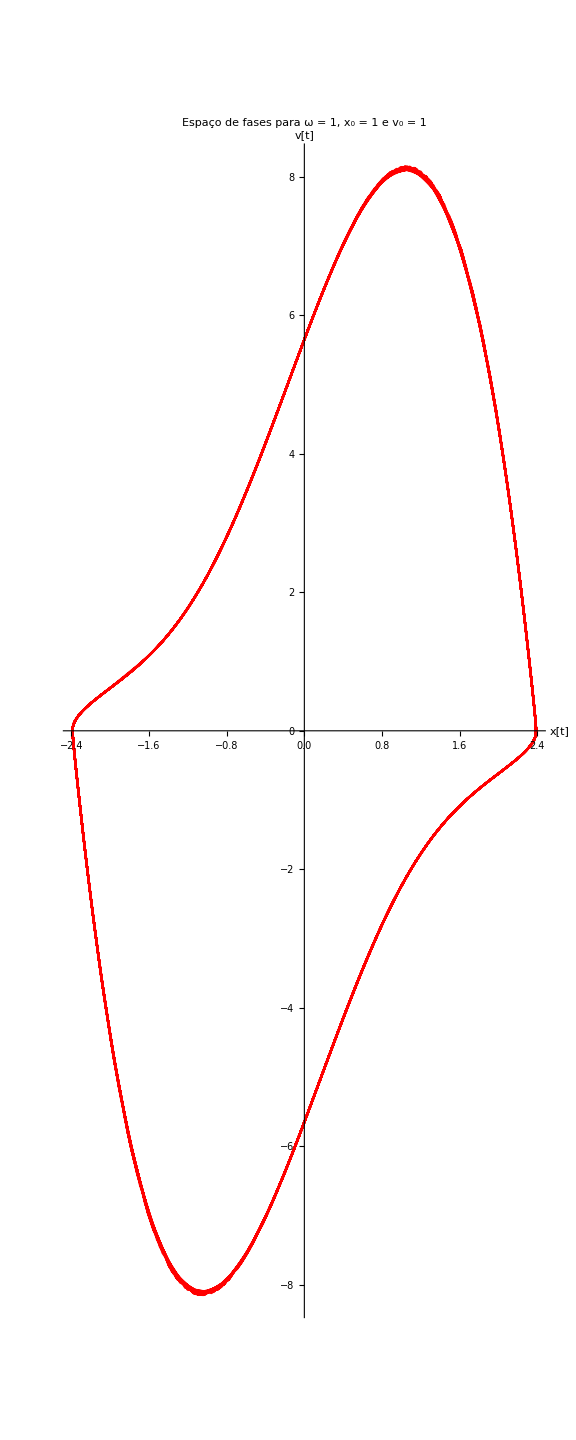

```mathematica
sol=resolveVanDerPol[1,1,1,2000];
ParametricPlot[
Evaluate[{x[t],x'[t]}/.sol],
{t,1900,2000},
PlotLabel->"Espaço de fases para ω = 1, x_0 = 1 e v_0 = 1",
Evaluate[optam],
AxesLabel->{"x[t]","v[t]"},
PlotStyle->Red,
PlotRange->All
]
```

```mathematica
(*Comportamento tipicamente periódico de ciclo 1: órbita fechada no espaço de fases*)
```

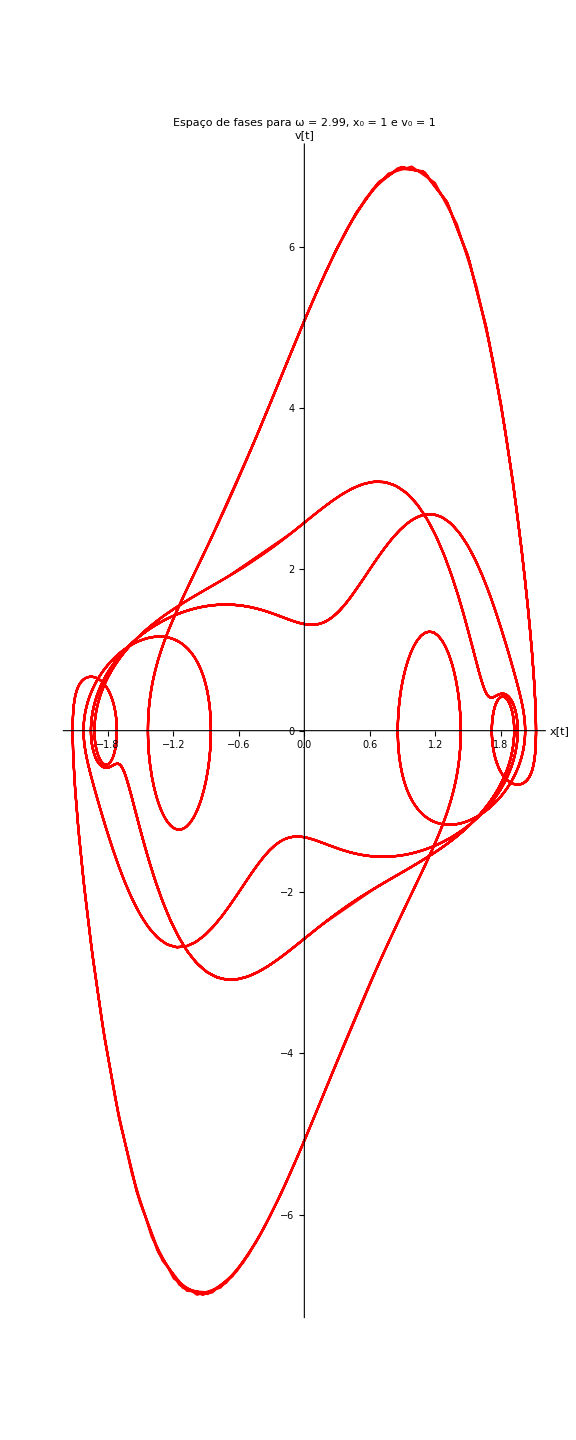

```mathematica
Clear[sol];
sol=resolveVanDerPol[2.99,1,1,2000];
ParametricPlot[
Evaluate[{x[t],x'[t]}/.sol],
{t,1900,2000},
PlotLabel->"Espaço de fases para ω = 2.99, x_0 = 1 e v_0 = 1",
Evaluate[optam],
AxesLabel->{"x[t]","v[t]"},
PlotStyle->Red,
PlotRange->All
]
```

```mathematica
(*Para ω = 2.99 já é possível verificar um comportamento mais próximo do que se esperaria de um sistema caótico.*)
```

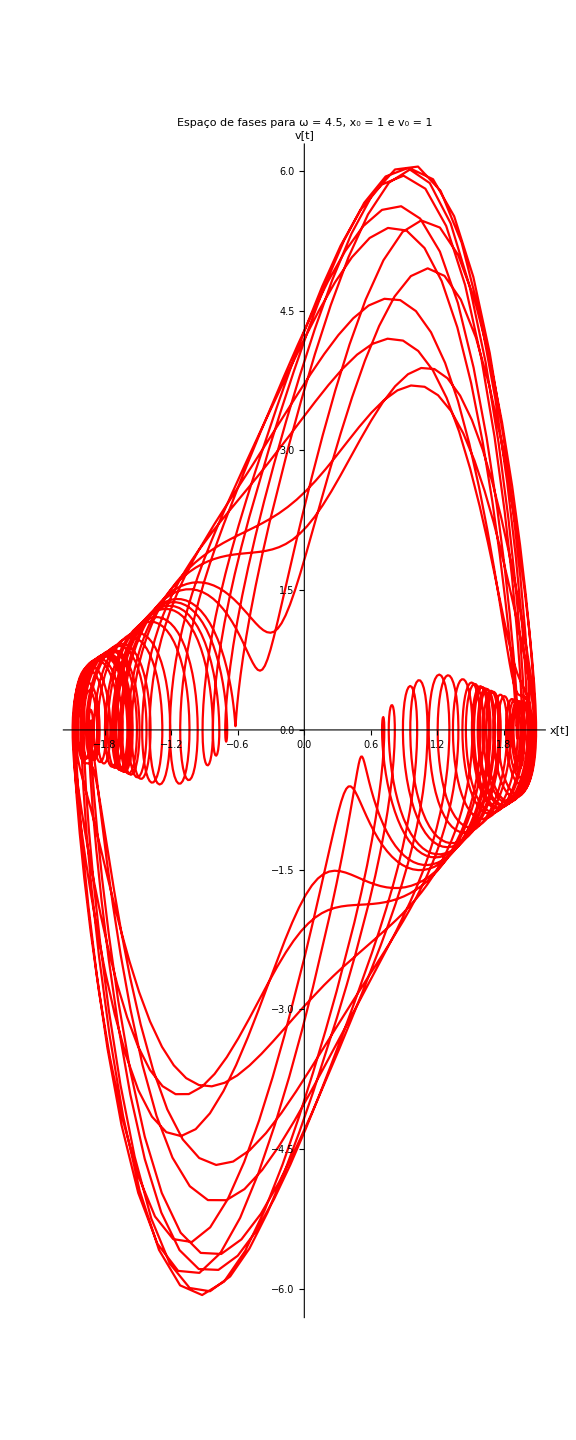

```mathematica
Clear[sol];
sol=resolveVanDerPol[4.5,1,1,2000];
ParametricPlot[
Evaluate[{x[t],x'[t]}/.sol],
{t,1900,2000},
PlotLabel->"Espaço de fases para ω = 4.5, x_0 = 1 e v_0 = 1",
Evaluate[optam],
AxesLabel->{"x[t]","v[t]"},
PlotStyle->Red,
PlotRange->All
]
```

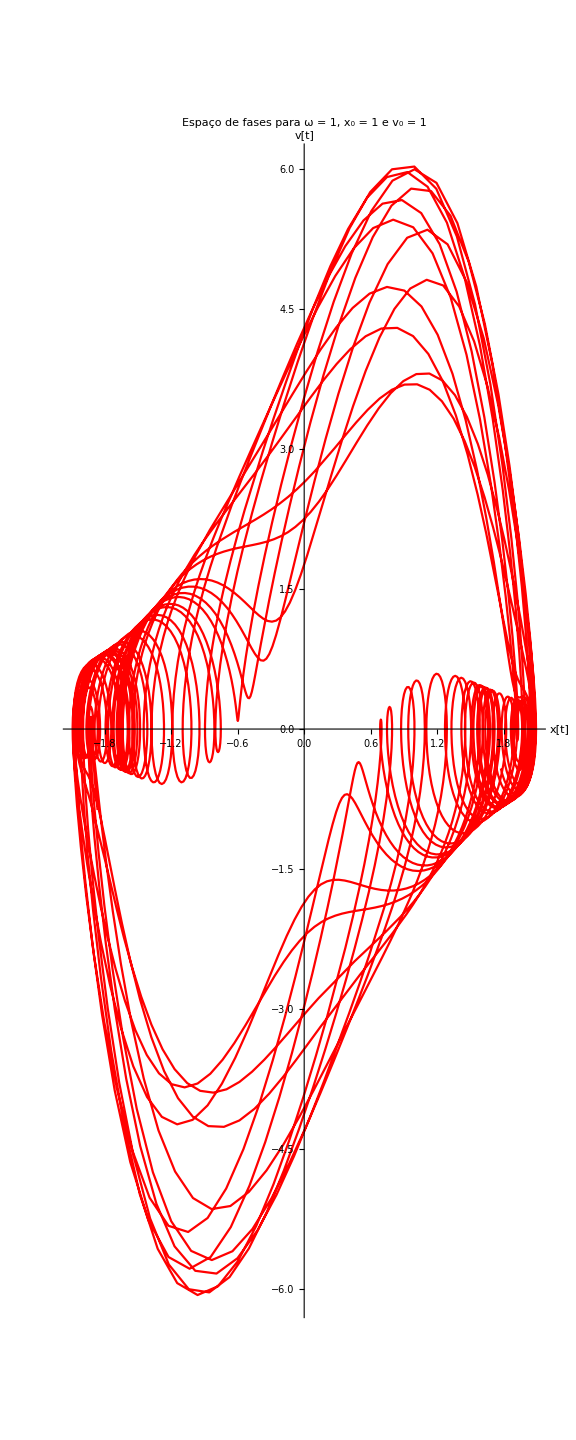

```mathematica
(*Para essa escolha de ω já é possível obervar um comportamento caótico. À primeira vista é impossível identificar aqualquer órbita fechada mesmo no intervalo de tempo suficientemente longo no qual estamos fazendo a análise.*)

(*Tento aumentar aumentar o intervalo de tempo da análise para identificar algum eventual comportamento periódico.*)
Clear[sol];
sol=resolveVanDerPol[4.5,1,1,4000];
ParametricPlot[
Evaluate[{x[t],x'[t]}/.sol],
{t,3900,4000},
PlotLabel->"Espaço de fases para ω = 4.5, x_0 = 1 e v_0 = 1",
Evaluate[optam],
AxesLabel->{"x[t]","v[t]"},
PlotStyle->Red,
PlotRange->All
]
```

```mathematica
(*De fato, temos um comportamento típicamente caótico.*)
```

```mathematica
Clear[sol]
```

```mathematica
(*Exercício 2*)
```

```mathematica
(*Começo definindo as funções necessárias.*)
```

```mathematica
pontos[ω_,n_,ndesc_,xx_,vv_]:=Module[{T,x0,v0,ponto,lista},
(
T=2π/ω/.pars ;
x0=xx; 
v0=vv; 
lista={};
Do[ 
(
ponto={x[T],x'[T]}/.NDSolve[{(m x''[t]==-k x[t]+a(1-x[t]^2)x'[t]+F0 Cos[ω t])/.pars,x[0]==x0,x'[0]==v0},x,{t,0,T}][[1]];
x0=ponto[[1]]; 
v0=ponto[[2]]; 
If[i>ndesc,AppendTo[lista,{ω,x0,v0}]] 
),{i,1,n}
];
lista
) 
]
```

```mathematica
varrepontos[ωmin_,ωmax_,nω_,n_,ndesc_,xx_,vv_]:=Module[{x,v,lista,grandelista},
(
x=xx;
v=vv; 
grandelista={}; 
Do[
(
lista=pontos[ω,n,ndesc,x,v];
AppendTo[grandelista,lista[[All,{1,2}]]];
x=lista[[-1,2]];  
v=lista[[-1,3]]
),{ω,ωmin,ωmax,(ωmax-ωmin)/(nω-1)}
];
Flatten[grandelista,1]
)
]
```

```mathematica
diagbifurca[ωmin_,ωmax_,nω_,n_,ndesc_,xx_,vv_]:=
ListPlot[varrepontos[ωmin,ωmax,nω,n,ndesc,xx,vv],Evaluate[optam],Axes->False,Frame->True,FrameLabel->{"ω","x"},PlotStyle-> PointSize[0.001],AspectRatio->1]
```

```mathematica
(*Construo o diagrama de bifurcações solicitado. Parâmetros: ωmin = 1, ωmax = 6, nω = 500, x[0] = 1, v[0] = 1. Por questões de desempenho computacional, utilizaremos n = 250 e ndesx = 100.*)
```

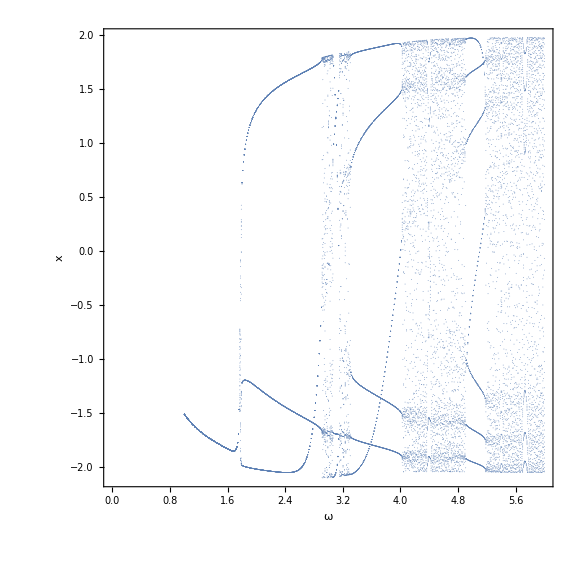

```mathematica
diagbifurca[1,6,500,50,10,1,1]
```

```mathematica
(*Exercício 3*)
```

```mathematica
(*Começo definindo as funções necessárias*)
```

```mathematica
poincare[ω_,n_,ndesc_,tam_]:=Module[{T,x0,v0,ponto,lista},
(
T=2π/ω/.pars ;
x0=0; 
v0=0; 
lista={};
Do[
(
ponto={x[T],x'[T]}/.NDSolve[{(m x''[t]==-k x[t]+a (1-x[t]^2) x'[t]+F0 Cos[ω t])/.pars,x[0]==x0,x'[0]==v0},x,{t,0,T}][[1]];
x0=ponto[[1]]; 
v0=ponto[[2]];
If[i>ndesc,AppendTo[lista,ponto]] 
),{i,1,n}
];
ListPlot[lista,Evaluate[optam],Axes->False,Frame->True,FrameLabel->{"x","v"},PlotStyle->PointSize[tam],AspectRatio->1]
) 
]
```

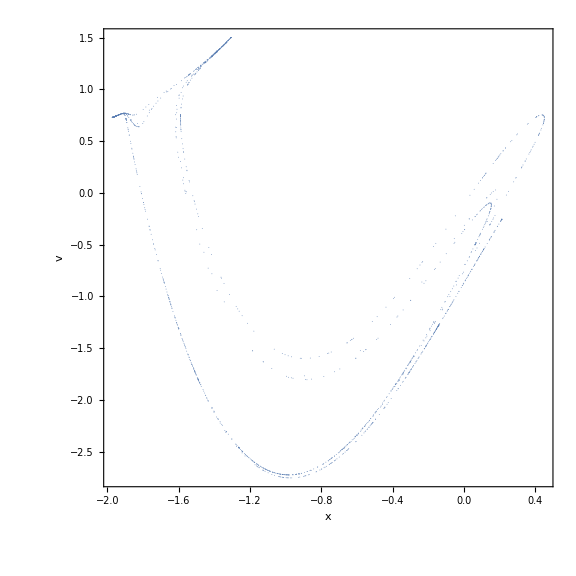

```mathematica
poincare[1.788,2500,500,0.001]
```

```mathematica
(*Aplico um zoom no gráfico anterior de tal maneira a evidnciar o caráter fractal do atrator encontrado.*)
```

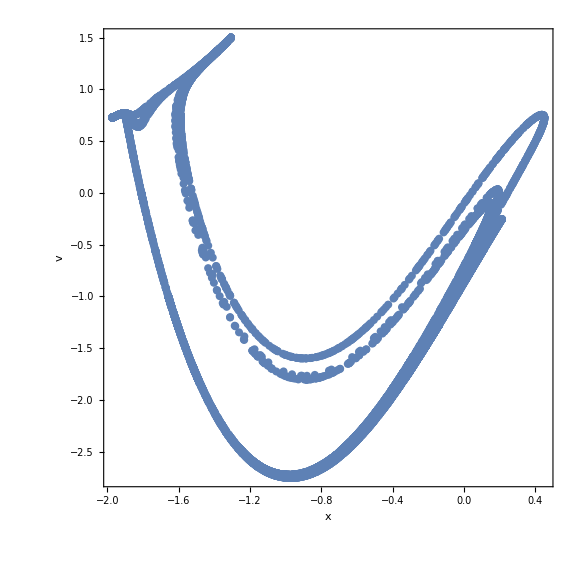

```mathematica
Show[poincare[1.788,9000+1000,1000,0.01],PlotRange->{{-1.1,-0.9},{-2.6,-2.8}}]
```

```mathematica
(*Obs.: Não foi possível elevar muito a quantidade de pontos / iterações e obter um comportamento mais próximo de um fractal devido ao baixo desempenho computacional da minha máquina.*)
```

```mathematica
(*Exercício 4*)
```

```mathematica
(*Obtenho a solução da equação para as duas condições iniciais distintas*)
```

```mathematica
ω=1.788;
sol1=NDSolve[{(m x''[t]==-k x[t]+a (1-x[t]^2) x'[t]+F0 Cos[ω t])/.pars,x[0]==0.4,x'[0]==0.1},x,{t,0,100}];
sol2=NDSolve[{(m x''[t]==-k x[t]+a (1-x[t]^2) x'[t]+F0 Cos[ω t])/.pars,x[0]==0.4+10^-8,x'[0]==0.1},x,{t,0,100}];
```

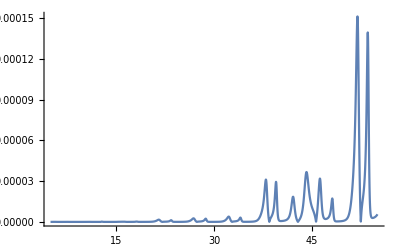

```mathematica
Plot[Abs[Evaluate[x[t]/.sol1]-Evaluate[x[t]/.sol2]],{t,5,55},PlotRange->All]
```

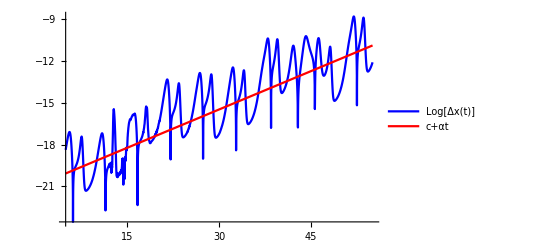

```mathematica
Plot[{Log[Abs[Evaluate[x[t]/.sol1]-Evaluate[x[t]/.sol2]]],(-21+0.184*t)},{t,5,55},PlotStyle->{Blue,Red},PlotLegends->{"Log[Δx(t)]","c+αt"}]
```

```mathematica
(*Uma vez que estamos lidando com resultados numéricos e as funções padrão de ajuste de curvas não podem ser aplicadas, foi feito uma estimativa da função ajuste c+αt para alguns valores distintos das constantes de interesse. 
Em meio aos testes, os parâmetros que se adequaram mais consistentemtene ao gráfico foram c = -20 e α = 0.184.
*)
```

```mathematica
(*A estimativa do coeficiente de Lyapunov, portanto, é 0.184. Esse valor é positivo, e isso significa que o sistema exibe sim uma dependência sensível nas condições iniciais. A conclusão obtida é perfeitamente consistente com os resultados anteriores; o gráfico Δx x t construído anteriormente de fato exibe discrepâncias muito significativas entre as soluções, principalmente após tempos muito longos de evolução do sistema.*)
```